# Introduction to Machine Learning (ML)

## Learning in general (humans, machines...)

Simple question: What do you see?

Strictly speaking, this is not a cat... but we identify it as a cat. 

Why?

Because we learnt how a cat looks like...

## The learning process

### Data storage

Observation, memory

Example: Observe many cats

### Abstraction

Concepts from data

Represent data in some useful way

Summarise the data using a model (e.g. a mathematical model)

The image of a cat represents much more than the raw data defining the image

### Generalisation

Being able to use abstract knowledge for future action

Select useful patterns in the abstracted knowledge to quickly identify new scenarios

Generalization allows us to identify a cat that we had not seen before, i.e. it is not in our data

### Evaluation

## Machine learning data bases

Data for machine learning can potentially be obtained from many sources. We will mostly use data from the following sources in this course:

Wolfram Data Repository - Curated data  - https://datarepository.wolframcloud.com/

Machine Learning Repository  - http://archive.ics.uci.edu/ml/index.php

Kaggle - https://www.kaggle.com/datasets

We will also use some data from my own research

## Example: Learning process for the law of free fall

The scientific method is a method of procedure that has characterized natural science since the 17th century, consisting in

systematic observation, measurement, and experiment and

the formulation, testing, and modification of hypotheses.

This example illustrates how the law of free fall can be derived from data following the scientific method. In fact, the scientific method leading to scientific theories can be viewed as a learning process for researchers.

### Data

The distance covered by an apple moving in free fall (no air resistance) is measured every second during 10 seconds.

```mathematica
data={{4.9,1},{19.7,2},{44.5,3},{78.8,4},{123.,5},{178.6,6},{245.,7},{317.5,8},{399.1,9},{495.9,10}};
TableForm[data,TableHeadings->{None,{"height (m)","Time (s)"}}]
```

height (m) | Time (s)
4.9 | 1
19.7 | 2
44.5 | 3
78.8 | 4
123. | 5
178.6 | 6
245. | 7
317.5 | 8
399.1 | 9
495.9 | 10

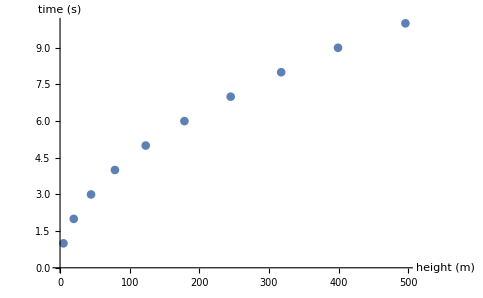

```mathematica
ListPlot[Transpose[Join[{height,time}]],AxesLabel->{"height (m)","time (s)"}]
```

### Abstraction - A model

Physics law:

h=1/2 gt^2        (g = 9.8 m/s^2)

represents an abstraction of the data.

The observed time, t, taken by the apple to move a distance h can be approximated by the formula 

t =√(2/g h)

Mathematica can also find an approximation to this law based on the data:

```mathematica
FindFormula[data, h]
```

0.448835 (Global`h)^0.5

Both the physics law and the formula found by Mathematica are approximations to the observed data.

Compare the predicted times tP and tM with the observed time

```mathematica
tP[h_]:=√(2/9.81 h);
tM[h_]:=0.448835 h^0.5;
```

```mathematica
TableForm[Table[{time[[t]],tP[height[[t]]],tM[height[[t]]]},{t,1,tmax}],TableHeadings->{None,{"observed time (s)","tP (s)","tM (s)"}}]
```

observed time (s) | tP (s) | tM (s)
1 | 0.99949 | 0.993539
2 | 2.00407 | 1.99214
3 | 3.01204 | 2.9941
4 | 4.00815 | 3.98428
5 | 5.00764 | 4.97782
6 | 6.03422 | 5.99829
7 | 7.06746 | 7.02538
8 | 8.04549 | 7.99758
9 | 9.02031 | 8.9666
10 | 10.0549 | 9.99502

### Generalisation

Observe the free fall of oranges, trucks, feathers, etc

Repeat the abstraction step for all of them. All compatible with the same model:

t =√(2/g h)

Conclude that all objects fall at the same pace (in the absence of air resistance)

### Evaluation

Repeat the experiment in different planets...

The law fails (g depends on the planet)

Refine the law:

t =√((2 R^2)/(G M) h)

where

R: radius of the planet

M: Mass of the planet

G: Gravitational constant

```mathematica
Entity["PhysicalConstant","GravitationalConstant"]["Value"]
```

6.674×10^-11 m^3/(kg s^2)

You may want to find the value of M and R for several planets and compare the free-fall times for different heights, h.

## Machine learning in practice

Five key steps:

### Data collection

Gather the learning material

```mathematica
images = {-Graphics-,-Graphics-,-Graphics-};
```

### Data exploration and preparation

Learn about the data through exploration

Data are numbers after all...

```mathematica
ImageData[images[[1]]]
```

{{{0.0705882,0.145098,0.027451},{0.0627451,0.12549,0.0235294},{0.027451,0.0745098,0.},144,{0.168627,0.380392,0.0509804},{0.156863,0.372549,0.0470588},{0.172549,0.388235,0.0627451}},111,{1}}
 |  |  |  |

One can go back from data to image

```mathematica
Image[ImageData[images[[1]]][[1;;10]]]
```

-Graphics-

Might require cleaning and reformatting data

Get an idea of what we can learn from the data. What questions to ask

Ex. Classify the images, identify groups of similar images, etc.

### Model training

Select an appropriate algorithm to learn from the data

Algorithm represents the data as a model

### Model evaluation

How well does the algorithm learns?

Possibly using a test dataset

Develop measures to quantify the performance

Example: Classify images

```mathematica
ImageIdentify[images]
```

{Japanese iris,European wildcat,person}

### Model improvement

Needed if performance is not good enough

Perhaps change the model

Perhaps use additional data

## Categories of machine learning

There are three main types of machine learning in terms of the model training step mentioned in the previous section.

Supervised machine learning: The algorithm learns from examples (i.e. labeled data).

Unsupervised machine learning: No teaching. The algorithm has to identify patterns and relationships on its own.

Reinforcement learning:

The algorithm learns to do something by being rewarded when successful and punished when unsuccessful.

For example, reinforcement learning is a popular method for computers to learn how to play board games or how to interact with an environment that is not known in advance (e.g. a maze).

It is not so relevant for data science.

The course will focus on supervised and unsupervised algorithms which are more relevant to data science.

### Supervised learning

Aim: Use a model to generate reasonable predictions for the response to new input data

-Graphics-


How? Training a computer using a known set of input data (a training set) and known responses to the data (output)

N_T (input, output) examples

-Graphics-

Two types of supervised learning: Classification and Prediction (Regression)

#### Classsification

Is this A or B? Class 1 or class 2 …

Spam or not?

Healthy tumour or cancerous...

A human from Europe or Middle East

Aim: Train a model to classify unseen data in a set of K classes, {C_k}_(k=1)^K. Use a training set consisting of N_T training examples belonging to K know classes, {C_k}_(k=1)^K .

-Graphics-

For instance, a Wolfram classifier trained to recognised images works as follows:

```mathematica
image=CurrentImage[]
ImageIdentify[CurrentImage[]]
```

-Graphics-

marker

#### Prediction (Regression)

How much or how many?

Price of a home…

Energy consumption in a building…

Aim: Train a model to predict a numerical response y for unseen data. Use a training set consisting of N_T training examples with known values for y.

-Graphics-

### Unsupervised learning

Aim: Discover relationships or patters from the data.

Useful to deal with data that is not labeled (i.e. when training data is not available)

How is the data organized?

Does the data have some inherent structure?

Do the samples sort themselves out into different groups and subgroups?

```mathematica
images = {-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-};
```

```mathematica
FindClusters[images,3]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

Use two dimensions to see the clusters

```mathematica
FeatureSpacePlot[images,LabelingFunction->(ImageResize[#,200]&)]
```

-Graphics-

```mathematica
FeatureSpacePlot[images]
```

-Graphics-

Task: Try to include your photo or photos of other objects to see in which cluster they are classified

## Machine learning and programming

Machine learning involves programming algorithms but it is different to traditional programming!!

#### Traditional programming to recognise images

Write a simple program to recognise the image of a person

```mathematica
images={LinguisticAssistant["Image"],LinguisticAssistant["Image"]}
```

{-Graphics-,-Graphics-}

```mathematica
programImage[image_]:=If[image==images[[1]]||image==images[[2]],"Person","Not recognised"];
```

```mathematica
programImage[-Graphics-]
```

Person

The program is not very smart: It will only recognise images used to train the program...

Let us try with another person

```mathematica
image2=CurrentImage[]
```

-Graphics-

```mathematica
programImage[image2]
```

Not recognised

#### Machine learning will recognise images that never saw before

Through training, machine learning algorithms identify key features of a generic person and can recognise new images. It learnt to identify!

```mathematica
ImageIdentify[-Graphics-]
```

person

You might suspect that Einstein’s images were used in the training dataset but... our current photo certainly wasn’t:

```mathematica
ImageIdentify[-Graphics-]
```

person